The governing nonlinear of the system 
φ_(,ξξ)-α^2φ +(β^2 α^2)/(1-φ)^3=0

```mathematica
(*Useful Modules*)
ClearAll["Global`*"]
Subscript[σ̃, c]=N[√27/256]

ϕf1[β_]:=x/.NSolve[{x-β^2/(1-x)^3==0 && 0<x<1},x][[1,1]];
ϕf2[β_]:=x/.NSolve[{x-β^2/(1-x)^3==0 && 0<x<1},x][[2,1]];
δ2Π1[βi_]:=Module[{β=βi},1-(3 β^2)/(1-ϕf1[β])^4];
δ2Π2[βi_]:=Module[{β=βi},1-(3 β^2)/(1-ϕf2[β])^4];
```

0.32476

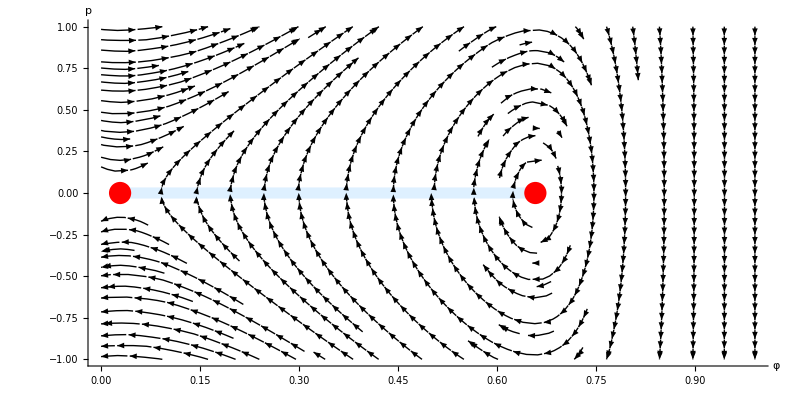

```mathematica
(*Phase Plane analysis*)
Block[{c=√27/256,α=√10,β=0.5 c},
pts=Flatten[Table[{{x,y},Gray},{x,0,1,0.1},{y,-1,1,0.2}],1];

Graphics[{PointSize[0.01],Pink,Point[{ϕf1[β],0}],Point[{ϕf2[β],0}]}];
S={ϕf1[β],0};
En={ϕf2[β],0};
PS=Point[{S}];
PEn=Point[{En}];
L=Line[{S,En}];
p1=Graphics[{PointSize[0.02],Red,PS,PEn}];
p2=Graphics[{Thickness[0.01],LightBlue,L}];
p3=StreamPlot[{p,α^2 ϕ-(β^2 α^2)/(1-ϕ)^3},{ϕ,0,1},{p,-1,1},
StreamPoints->Fine,
StreamStyle->Black,
(*StreamPoints->{pts,Automatic,Scaled[2.3]},*)
StreamScale->0.05,
(*Epilog->{Blue,PointSize[Medium],Point[pts[[All,1]]]}*)
WorkingPrecision->60,
(*AxesStyle->Directive[Gray,Thickness[0.001],FontFamily->"Helvetica"],*)
Axes->True,
(*AspectRatio->2,*)
ImageSize->800,
GridLines->None,
Ticks->Automatic,
(*StreamStyle->Pink,*)
AxesLabel->{
Style["φ ",Black,FontFamily->"TimesNewRoman",30],
Style["p",Black,FontFamily->"TimesNewRoman",30]},
Frame->False,
FrameLabel->{
Style["φ ",Black,FontFamily->"TimesNewRoman",16],
Style["p",Black,FontFamily->"TimesNewRoman",16]},
(*AxesOrigin->{0,0},*)
(*Mesh->1000,*)
(*PerformanceGoal->"Quality",*)
AxesStyle->Directive[Black,Thickness[0.001],FontFamily->"Times New Roman",18]];

(*Slabel=Style["S",Black,FontFamily->"Times",24, Italic];
Elabel=Style["E",Black,FontFamily->"Times",24, Italic];
p5=Graphics[Text[Slabel,{ϕf1,0}]];
*)
PPP=Show[ p3,p2,p1,PlotRange->All,AspectRatio->1/2]
]
```

```mathematica
Export["~/Dropbox/HKResearch/StudentsResearch/Kaushik/bifurcation_type_behavior_pfm/Haneesh/Notes/Figures/PPP.pdf",PPP]
```

~/Dropbox/HKResearch/StudentsResearch/Kaushik/bifurcation_type_behavior_pfm/Haneesh/Notes/Figures/PPP.pdf

(3 √3)/16

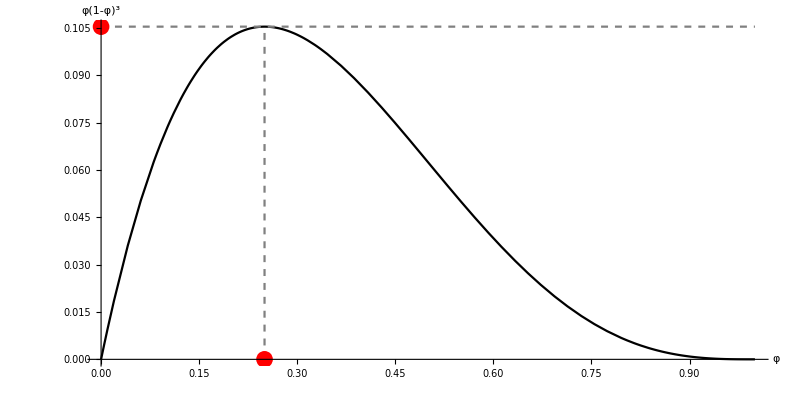

~/Dropbox/HKResearch/StudentsResearch/Kaushik/bifurcation_type_behavior_pfm/Haneesh/Notes/Figures/Solution.pdf

```mathematica
(*Theoretical strength*)
ClearAll[P1,P2,p1,p2,p3];
Maximize[{ϕ(1-ϕ)^3,0≤ϕ≤ 1},ϕ];
c=√27/256
P1={0,c^2};
P2={1/4,0};
p1=Graphics[{PointSize[0.015],Red,Point[{P1}],Point[{P2}]}];
p3=ParametricPlot[{{ϕ,ϕ (1-ϕ)^3},{ϕ,27/256},{1/4,27/256 ϕ}},{ϕ,0,1},
PlotStyle->{Black,{Gray,Dashed},{Gray,Dashed}},AspectRatio->1,
Axes->True,
AxesLabel->{
Style["φ",Black,FontFamily->"TimesNewRoman",30],
Style["φ(1-φ)^3 ",Black,FontFamily->"TimesNewRoman",30]},

(*AspectRatio->2,*)
ImageSize->800,
GridLines->None,
Ticks->Automatic,
AxesStyle->Directive[Black,Thickness[0.001],FontFamily->"Times New Roman",18]
];
Solution=Show[ p3,p1,PlotRange->All,AspectRatio->1/2]
Export["~/Dropbox/HKResearch/StudentsResearch/Kaushik/bifurcation_type_behavior_pfm/Haneesh/Notes/Figures/Solution.pdf",Solution]
```

```mathematica
Series[(ϕ-β^2/(1-ϕ)^3)/.ϕ->ϕ0+δϕ,{δϕ,0,1}]
```

(β^2/(-1+ϕ0)^3+ϕ0)+(1-(3 β^2)/(-1+ϕ0)^4) δϕ+O[δϕ]^2

Pattern selection: what is the period?
The strength of the solid is β=27/256=0.106

```mathematica
(256)^(1/2)
```

16

```mathematica
Animate[Block[{α=Sqrt[10],β=0.1(27 α^2)/256,t=5},sol=NDSolve[{ϕ''[ξ]-α^2 ϕ[ξ]+β/(1-ϕ[ξ])^3==0,ϕ[0]==ϕ0,ϕ'[0]==0},ϕ[ξ],{ξ,0,t}];
Plot[{Evaluate[ϕ[ξ]/.sol[[1]]],1},{ξ,0.0,t},PlotRange->{{0,t},{0,1}}]
],{ϕ0,0.0,1}]
```

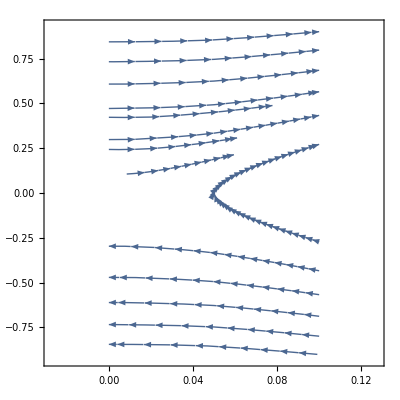

```mathematica
Block[{c=√(27/256),α=√10,β=0.99c},
(*g[ϕ_]=2 ϕ^3-3 ϕ^2+1;*)
g[ϕ_]=1-Exp[-10(1-ϕ)];

StreamPlot[{p,α^2 ϕ+(g'[ϕ] α^2 β^2)/g[ϕ]^2},{ϕ,0.,.1},{p,-0.9,0.9},StreamPoints->Automatic]
]
```

```mathematica
p[x_]=a x^3+b x^2+c x+d
Solve[{p[0]==1 && p[1]==0 && p'[0]==0 && p'[1]==0},{a,b,c,d}]
```

d+c x+b x^2+a x^3

{{a→2,b→-3,c→0,d→1}}

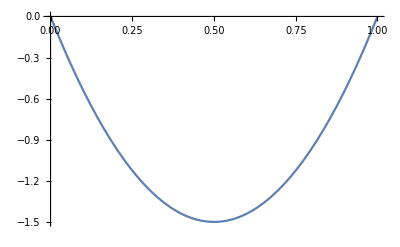

```mathematica
ps[x_]=2 x^3-3 x^2+1;
Plot[ps'[x],{x,0,1}]
```

```mathematica
RΠ[γ_]:=-1/γ(ϕf[γ]^2-γ/(1-ϕf[γ])^2);
```

```mathematica
Plot[δ2Π1[x],{x,0.001,√(27/256)},PlotStyle->{Dashed}]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ReplaceAll::reps: {{} ⟦ 1, 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics-

```mathematica
f[27/256]
```

{ϕ→0.25}

```mathematica
Clear[ϕ]
NSolve[{x-0.09/(1-x)^3==0 && 0<x<1},x][[1]]
```

{x→0.382807}

```mathematica
N[27/256]
```

0.105469

```mathematica
Series[1/(1-ϕf-Δϕ)^2,{Δϕ,0,2}]
```

1/(1-ϕf)^2-(2 Δϕ)/(-1+ϕf)^3+(3 Δϕ^2)/(-1+ϕf)^4+O[Δϕ]^3

```mathematica
DSolve[{ϕ''[ξ]-α^2 ϕ[ξ]==0,ϕ'[0]==0,ϕ[1]==1},ϕ[ξ]]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

```mathematica
sol2=DSolve[{-α^2 ϕ[ξ]+ϕ''[ξ]==0,ϕ'[0]==0,ϕ[1]==1},ϕ,ξ]
```

{{ϕ→Function[{ξ},(ⅇ^(α-α ξ) (1+ⅇ^(2 α ξ)))/(1+ⅇ^(2 α))]}}

```mathematica
ϕb[ξ_]=ϕ[ξ]/.sol2[[1]];
ϕt[ξ_]=1;
```

```mathematica
Πt[ϕ_,α_,β_]=Module[{αs=α,βs=β,ϕs=}
NIntegrate[ϕ'[ξ]^2+α^2 ϕ[ξ]^2-(β^2 α^2)/(1-ϕ[ξ])^2,{ξ,0,1}]
```

```mathematica
Π[ϕb,1]
```

NIntegrate::inumr: The integrand ⅇ^2\ α - 2\ α\ ξ\ (1 + ⅇ^2\ α\ ξ)^2/(1 + ⅇ^2\ α)^2 + (2\ ⅇ^α « 1 » α « 1 » « 1 »\ α/1 + ⅇ^« 1 » - ⅇ^« 1 »\ (« 1 »)\ α/1 + ⅇ^« 1 »)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate[ϕb'[ξ]^2+1^2 ϕb[ξ]^2,{ξ,0,1}]

```mathematica
Πt[ϕt,0.1,0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate[ϕt'[ξ]^2+0.1^2 ϕt[ξ]^2-(0^2 0.1^2)/(1-ϕt[ξ])^2,{ξ,0,1}]

```mathematica
Plot[NSolve[{x-β^2/(1-x)^3==0 && 0<x<1},x],{β,0,(3√3)/16}]
```

-Graphics-

```mathematica
Block[{β=0.01},
sol=NSolve[{x-β^2/(1-x)^3==0 && 0<x<1},x];
sol[[2,1]];
sol[[1,1]]]
```

x→0.95283

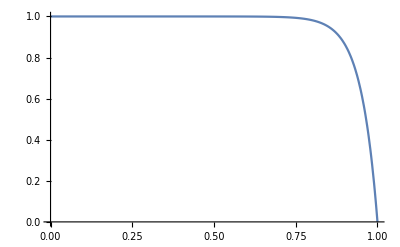

```mathematica
Plot[1-Exp[-(1-x)/0.05],{x,0,1},PlotRange->All]
```